```mathematica
BinInt[xmin_,xmax_ ]:=NIntegrate[ⅇ^(-x/1.5),{x,xmin,xmax}]
```

```mathematica
arr=Range[-3,1,1/25];
```

```mathematica
exparr=ⅇ^#&/@arr//N;
```

```mathematica
exparr//N
```

{0.0497871,0.0518189,0.0539337,0.0561348,0.0584257,0.0608101,0.0632918,0.0658748,0.0685632,0.0713613,0.0742736,0.0773047,0.0804596,0.0837432,0.0871609,0.090718,0.0944202,0.0982736,0.102284,0.106459,0.110803,0.115325,0.120032,0.12493,0.130029,0.135335,0.140858,0.146607,0.15259,0.158817,0.165299,0.172045,0.179066,0.186374,0.19398,0.201897,0.210136,0.218712,0.227638,0.236928,0.246597,0.256661,0.267135,0.278037,0.289384,0.301194,0.313486,0.32628,0.339596,0.353455,0.367879,0.382893,0.398519,0.414783,0.431711,0.449329,0.467666,0.486752,0.506617,0.527292,0.548812,0.571209,0.594521,0.618783,0.644036,0.67032,0.697676,0.726149,0.755784,0.786628,0.818731,0.852144,0.88692,0.923116,0.960789,1.,1.04081,1.08329,1.1275,1.17351,1.2214,1.27125,1.32313,1.37713,1.43333,1.49182,1.55271,1.61607,1.68203,1.75067,1.82212,1.89648,1.97388,2.05443,2.13828,2.22554,2.31637,2.4109,2.50929,2.6117,2.71828}

```mathematica
mixedarr=Transpose[{exparr[[1;;-2]],exparr[[2;;-1]]}];
```

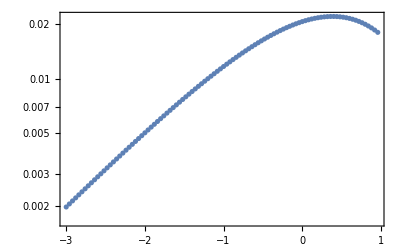

```mathematica
ListLogPlot[Transpose[{arr[[1;;-2]],BinInt@@@mixedarr}],Frame-> True]
```